# Lab 8: 2D Geometric Transformations

## Computer Graphics Lab, Wolfram Mathematica

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->True];
```

```mathematica
SetOptions[{Plot,Plot3D,ContourPlot,ContourPlot3D, DensityPlot,ParametricPlot,ParametricPlot3D,ListPlot,ListLinePlot,ListPointPlot3D,Graphics,Graphics3D,PolarPlot}, ImageSize->Small,AxesLabel->{"x","y","z"}];
```

```mathematica
(* Problem 1 Rotate an equilateral triangle RT=2 at the distance RR=7/2 from the origin. Rotate the triangle around itself.
The code highlighted by Cyan is attached to the Lab manual.
*)
```

```mathematica
RT1=2; RR=7/2;Rad1={RR,0};
```

```mathematica
(* Center *)
```

```mathematica
CentRot1={0,0};
```

```mathematica
OTri1=RegularPolygon[CentRot1,RT1,3]
```

RegularPolygon[{0,0},2,3]

```mathematica
(* Center point  *)
```

```mathematica
OCent1={Red,Point[CentRot1]}
```

{RGBColor[1, 0, 0],Point[{0,0}]}

```mathematica
(* The Triangle and the center point *)
```

```mathematica
O1={OTri1,OCent1}
```

{RegularPolygon[{0,0},2,3],{RGBColor[1, 0, 0],Point[{0,0}]}}

```mathematica
(* ATTN: Compose the rotation function *)
```

```mathematica
ORot1[a_]:=GeometricTransformation[O1,Composition[RotationTransform[a],TranslationTransform[Rad1]]]
```

```mathematica
(* Define the graphics function  *)
```

```mathematica
GTri1[a_]:=Graphics[ORot1[a],Axes->True, AxesOrigin->{0,0},PlotRange->5.5]
```

```mathematica
(* Check  *)
```

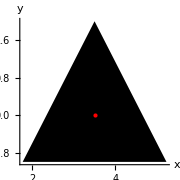
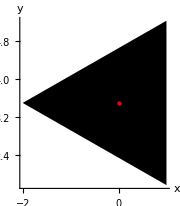
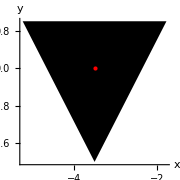
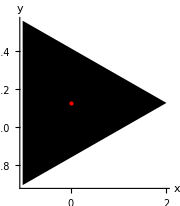
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[GTri1[a],{a,0,2Pi,Pi/2}]
```

```mathematica
OCir1:={Red,Circle[CentRot1,RR]}
```

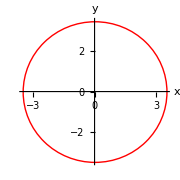

```mathematica
GCir1=Graphics[OCir1,Axes->True, AxesOrigin->{0,0},PlotRange->5.5]
```

```mathematica
(* Animate triangle moving along the circular trajectory with the radius 7/2. Display the Circle[RR[[1]]]  *)
```

```mathematica
OT1[t_]:=Graphics[{ORot1[t],OCir1},Axes->True, AxesOrigin->{0,0},PlotRange->5.5]
```

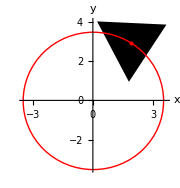

```mathematica
OT1[1]
```

```mathematica
Manipulate[OT1[t],{t,0,2Pi,0.1}]
```

```mathematica
ORot2[a_]:=GeometricTransformation[O1,Composition[RotationTransform[a],TranslationTransform[Rad1],RotationTransform[a]]]
```

```mathematica
GTri2[a_]:=Graphics[ORot2[a],Axes->True, AxesOrigin->{0,0},PlotRange->5.5]
```

```mathematica
OT2[t_]:=Graphics[{ORot2[t],OCir1},Axes->True, AxesOrigin->{0,0},PlotRange->5.5]
```

```mathematica
Manipulate[OT2[t],{t,0,2Pi,0.1}]
```

```mathematica
(* Problem 2 *)
```

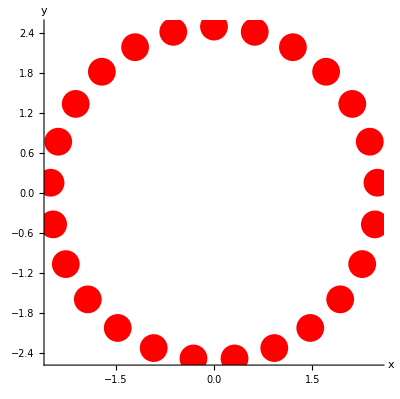

```mathematica
Graphics[{Red,PointSize[0.05],Point[CirclePoints[2.5,25]]},ImageSize->Tiny,Axes->True]
```

```mathematica
Points={Red,PointSize[0.05],Point[CirclePoints[2.5,10]]}
```

{RGBColor[1, 0, 0],PointSize[0.05],Point[{{0.772542,-2.37764},{2.02254,-1.46946},{2.5,0.},{2.02254,1.46946},{0.772542,2.37764},{-0.772542,2.37764},{-2.02254,1.46946},{-2.5,3.06162×10^-16},{-2.02254,-1.46946},{-0.772542,-2.37764}}]}

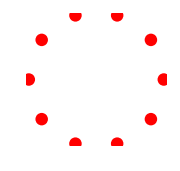

```mathematica
Graphics[Points]
```

```mathematica
RotPoints[a_]:=GeometricTransformation[Points,Composition[RotationTransform[a],TranslationTransform[Rad1],RotationTransform[a]]]
```

```mathematica
GPoints[a_]:=Graphics[RotPoints[a],Axes->True, AxesOrigin->{0,0},PlotRange->6]
```

```mathematica
Manipulate[GPoints[t],{t,0,2Pi,0.1}]
```

```mathematica
OTPoints[t_]:=Graphics[{RotPoints[t],OCir1},Axes->True, AxesOrigin->{0,0},PlotRange->6]
```

```mathematica
Manipulate[OTPoints[t],{t,0,2Pi,0.1}]
```

```mathematica
P1=1.0*CirclePoints[RT1,10]
```

{{0.618034,-1.90211},{1.61803,-1.17557},{2.,0.},{1.61803,1.17557},{0.618034,1.90211},{-0.618034,1.90211},{-1.61803,1.17557},{-2.,0.},{-1.61803,-1.17557},{-0.618034,-1.90211}}

```mathematica
nCP1=Dimensions[P1][[1]]
```

10

```mathematica
PointsC1={PointSize[0.08],Point[P1,VertexColors->RandomColor[nCP1]]}
```

{PointSize[0.08],Point[{{0.618034,-1.90211},{1.61803,-1.17557},{2.,0.},{1.61803,1.17557},{0.618034,1.90211},{-0.618034,1.90211},{-1.61803,1.17557},{-2.,0.},{-1.61803,-1.17557},{-0.618034,-1.90211}},VertexColors→{RGBColor[0.47886008840170313, 0.4992075663278923, 0.9433729991511299],RGBColor[0.031195701146507382, 0.3953911698141308, 0.5337635436798718],RGBColor[0.47183063799396896, 0.7560217544663459, 0.3326436838618472],RGBColor[0.3691416104805163, 0.7091474514865472, 0.04215763407439277],RGBColor[0.6266589206219502, 0.9339641814393771, 0.7414593663103972],RGBColor[0.8888832880073978, 0.6025468694754608, 0.5141444401024822],RGBColor[0.5576852527476293, 0.4444298315449109, 0.23919562650754322],RGBColor[0.5148460828654693, 0.7136103138820624, 0.718221261381516],RGBColor[0.8730844902340649, 0.7152745498650819, 0.6102430782788322],RGBColor[0.49426182613413316, 0.8582223913498388, 0.3020842138190074]}]}

```mathematica
RotPointsC1[a_]:=GeometricTransformation[PointsC1,Composition[RotationTransform[a],TranslationTransform[Rad1],RotationTransform[a]]]
```

```mathematica
GPoints1[a_]:=Graphics[RotPointsC1[a],Axes->True, AxesOrigin->{0,0},PlotRange->6]
```

```mathematica
Manipulate[GPoints1[t],{t,0,2Pi,0.1}]
```

```mathematica
GAll[t_]:=Show[{GPoints1[t],OT1[t]}]
```

```mathematica
Manipulate[GAll[t],{t,0,2Pi,0.1}]
```

```mathematica
Rot1[O_,R_,a_]:=Module[{ORot,GrO,a1},
ORot[a1_]:=GeometricTransformation[O,Composition[RotationTransform[a],TranslationTransform[{R,0}]]];
GrO[a1_]:=Graphics[ORot[a1],Axes->True,AxesOrigin->{0,0},PlotRange->5.5];
GrO[a]]
```

```mathematica
Rot1F[O_,R_]:=Module[{ORot,GrO,a1},
ORot[a1_]:=GeometricTransformation[O,Composition[RotationTransform[a1],TranslationTransform[{R,0}]]];
GrO[a1]:=Graphics[ORot[a1],Axes->True,AxesOrigin->{0,0},PlotRange->5.5];
GrO]
```

```mathematica
Disk1={Red,Disk[{0,0},1.5]}
```

{RGBColor[1, 0, 0],Disk[{0,0},1.5]}

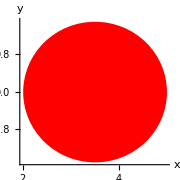
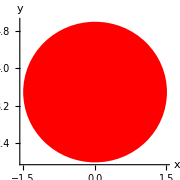
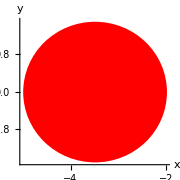
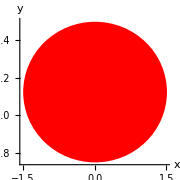
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Rot1[Disk1,RR,a],{a,0,2Pi,Pi/2}]
```

```mathematica
Manipulate[Rot1[Disk1,RR,a],{a,0,2Pi,Pi/4}]
```

```mathematica
(*Problem 3.1*)
```

```mathematica
O3={Blue,RegularPolygon[2,4]};
```

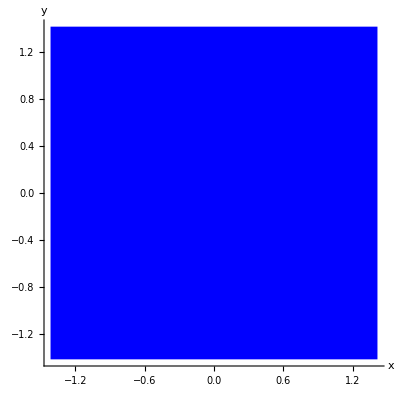

```mathematica
Graphics[O3,ImageSize->Tiny,Axes->True]
```

```mathematica
CenterRot={5,5};RD={4,0};
```

```mathematica
Dist=CenterRot+RD;
```

```mathematica
O3Zero={Red, PointSize[0.02],Point[{0,0}]};
```

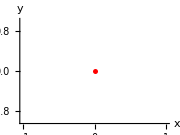

```mathematica
Graphics[O3Zero,Axes->True]
```

```mathematica
O3Trans=GeometricTransformation[O3,TranslationTransform[Dist]];
```

```mathematica
OCenter3={Orange,PointSize[0.08],Point[CenterRot]};
```

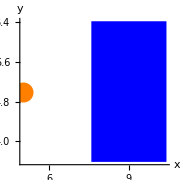

```mathematica
Graphics[{O3Trans,OCenter3},Axes->True,PlotRange->10]
```

```mathematica
ORot3[a_]:=GeometricTransformation[{O3,O3Zero}, Composition[RotationTransform[a,CenterRot],TranslationTransform[Dist]]];
```

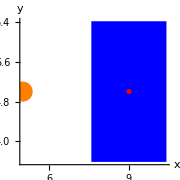
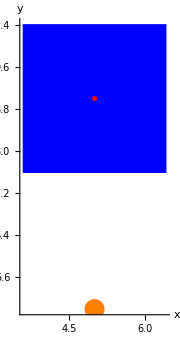
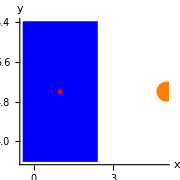
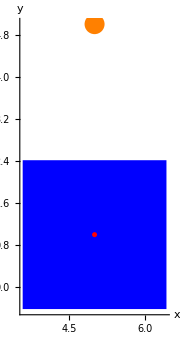
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics[{ORot3[a],OCenter3},Axes->True,PlotRange->10],{a,0,2Pi,Pi/2}]
```

```mathematica
GORot3[a_]:=Graphics[{ORot3[a],OCenter3},Axes->True,PlotRange->10]
```

```mathematica
Manipulate[GORot3[a],{a,0,2Pi}]
```

```mathematica
(* Problem 3.2 *)
```

```mathematica
T3[t_]:=0.1{t*Cos[t],2*t*Sin[t]}
```

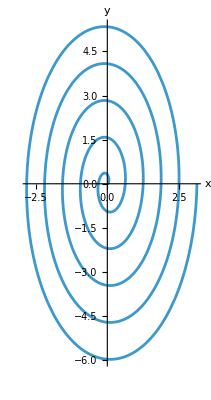

```mathematica
PT3=ParametricPlot[T3[t],{t,0,10Pi},ImageSize->Tiny]
```

```mathematica
OT3=PT3[[1]]
```

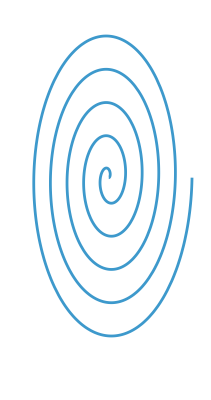

```mathematica
Graphics[OT3,ImageSize->Tiny]
```

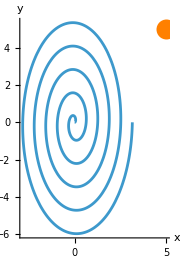

```mathematica
Graphics[{OT3,OCenter3},Axes->True,PlotRange->10]
```

```mathematica
OT3
```

```mathematica
OCenter3
```

{RGBColor[1, 0.5, 0],PointSize[0.08],Point[{5,5}]}

```mathematica
ORot4[a_]:=GeometricTransformation[OT3, Composition[RotationTransform[a,CenterRot],TranslationTransform[Dist],RotationTransform[a]]]
```

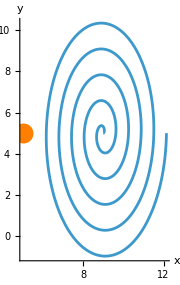
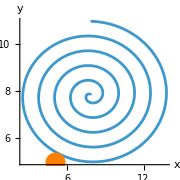
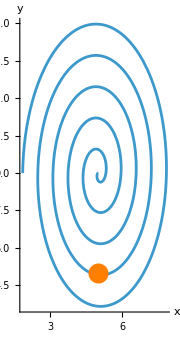
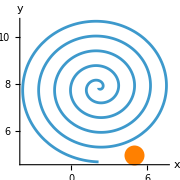
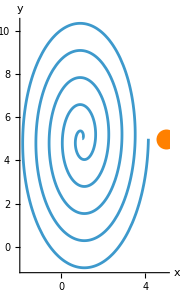
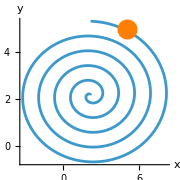
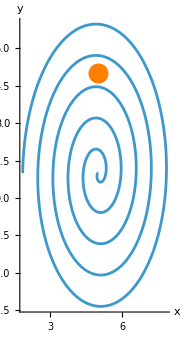
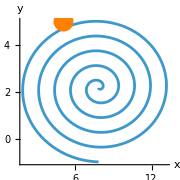
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics[{ORot4[a],OCenter3},Axes->True,PlotRange->10],{a,0,2Pi,Pi/4}]
```

```mathematica
G3[a_]:=Graphics[{ORot4[a],OCenter3},Axes->True,PlotRange->10]
```

```mathematica
Manipulate[G3[a],{a,0,2Pi}]
```

```mathematica
(* Problem 4 *)
```

```mathematica
Clear[Ob]
```

```mathematica
Ob[t_]:=4{Cos[2t],Sin[4t]}
```

```mathematica
Traj[t_]:={t,0.05t^2}
```

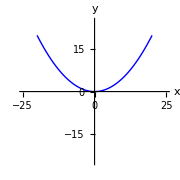

```mathematica
Tra=ParametricPlot[Traj[t],{t,-20,20},PlotRange->25,PlotStyle->{Blue,Thick}]
```

```mathematica
OTra=Tra[[1]];
```

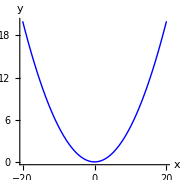

```mathematica
Graphics[OTra,Axes->True]
```

```mathematica
Curve[t_]:={4Cos[2t],4Sin[4t]}
```

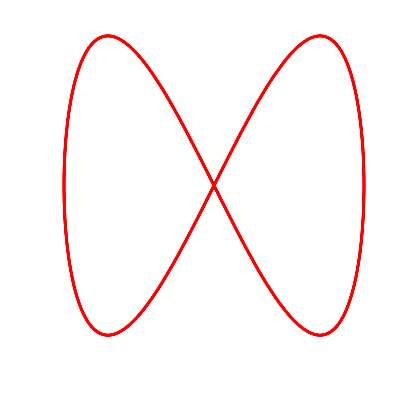

```mathematica
P=ParametricPlot[Curve[t],{t,0,2Pi},PlotStyle->Red,Axes->False,ImageSize->Tiny]
```

```mathematica
a=Pi/2
```

π/2

```mathematica
MTran[t_,a_]:=Composition[TranslationTransform[Traj[t]],RotationTransform[a]]
```

```mathematica
Ob=P[[1]];
```

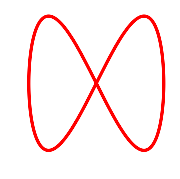

```mathematica
Graphics[Ob]
```

```mathematica
Trans[t_,a_]:=GeometricTransformation[Ob,MTran[t,a]]
```

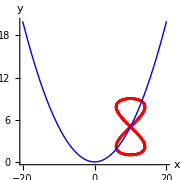

```mathematica
G1=Graphics[{Trans[10,Pi/2],OTra},Axes->True,PlotRange->40]
```

```mathematica
GTransAll[t_]:=Graphics[{Trans[t,t],OTra},Axes->True,PlotRange->40]
```

```mathematica
Manipulate[GTransAll[t],{t,-20,20}]
```

```mathematica
TransNew[t_,a_,b_]:=GeometricTransformation[{OTra,Trans[t,a]}, RotationTransform[b]]
```

```mathematica
GTransAllNew[t_]:=Graphics[TransNew[t,t,20+t],Axes->True,PlotRange->40]
```

```mathematica
Manipulate[GTransAllNew[t],{t,-20,20}]
```

```mathematica
(* Problem 5 *)
```

```mathematica
Rot2[ONew_,OTNew_,Traj_,t_,a_]:=Module[{MTran,t1,a1,Trans,G1},
MTran[t1_,a1_]:=Composition[TranslationTransform[Traj[t1]],RotationTransform[a1]];
Trans[t1_,a1_]:=GeometricTransformation[ONew,MTran[t1,a1]];
G1[t1_,a1_]:=Graphics[{Trans[t1,a1],OTNew},Axes->True,PlotRange->60];
G1]
```

```mathematica
M2=Rot2[Ob,OTra,Traj,t,a]
```

G1$14351

```mathematica
Manipulate[M2[t,t],{t,-20,20}]
```

```mathematica
(* Problem 6.1 *)
```

```mathematica
a=40
b=0.5
```

40

0.5

```mathematica
TrajNew[t_]:=a{Cos[2t],Sin[4t]}
ObNew[s_]:=b{s,0.05s^2}
```

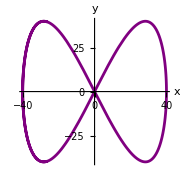

```mathematica
Try1=ParametricPlot[TrajNew[t],{t,-2,2},PlotStyle->Purple]
```

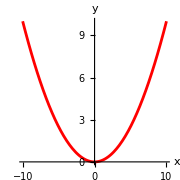

```mathematica
Try2=ParametricPlot[ObNew[t],{t,-20,20},PlotStyle->Red]
```

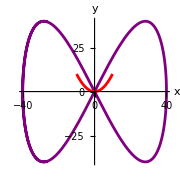

```mathematica
Show[{Try1,Try2}]
```

```mathematica
pp61=ParametricPlot[ObNew[t],{t,-20,20},PlotStyle->Red]
```

-Graphics-

```mathematica
o61=pp61[[1]];
```

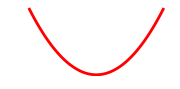

```mathematica
Graphics[o61]
```

```mathematica
pp62=ParametricPlot[TrajNew[t],{t,-2,2},PlotStyle->Purple]
```

-Graphics-

```mathematica
o62=pp62[[1]];
```

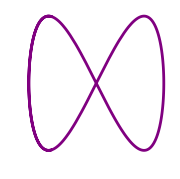

```mathematica
Graphics[o62]
```

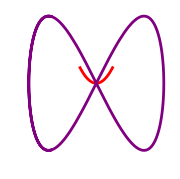

```mathematica
Graphics[{o61,o62}]
```

```mathematica
M6=Rot2[o61,o62,TrajNew,t,a]
```

G1$15032

```mathematica
Manipulate[M6[t/10,t],{t,-20,20}]
```

```mathematica
(* Problem 7 - Bonus *)
```

```mathematica
Rot5[O1_,O2_,OTraj_,Traj_,trange_]:=Module[{TAll,MTran1,MTran2,Trans1,Trans2,t1,a1,GAll},
MTran1[t1_,a1_]:=Composition[TranslationTransform[Traj[-t1+trange]],RotationTransform[a1]];
Trans1[t1_,a1_]:=GeometricTransformation[O1,MTran1[t1,a1]];

MTran2[t1_,a1_]:=Composition[TranslationTransform[Traj[t1-trange]],RotationTransform[a1]];
Trans2[t1_,a1_]:=GeometricTransformation[O2,MTran2[t1,a1]];

GAll[t1_,a1_]:=Graphics[{Trans1[t1,a1],Trans2[t1,a1],OTraj},Axes->True,PlotRange->60];

GAll]
```

```mathematica
pp71={Red,RegularPolygon[{0,0},20,4]}
```

{RGBColor[1, 0, 0],RegularPolygon[{0,0},20,4]}

```mathematica
pp72={Blue,RegularPolygon[{0,0},20,6]}
```

{RGBColor[0, 0, 1],RegularPolygon[{0,0},20,6]}

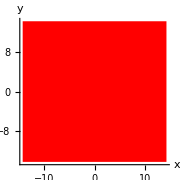

```mathematica
Graphics[pp71,PlotRange->40,Axes->True]
```

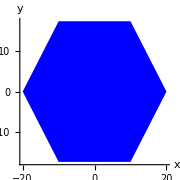

```mathematica
Graphics[pp72,PlotRange->40,Axes->True]
```

```mathematica
trange=20
```

20

```mathematica
M7=Rot5[pp71,pp72,o62,TrajNew,trange]
```

GAll$15493

```mathematica
Manipulate[M7[t/5,t],{t,-20,20}]
```

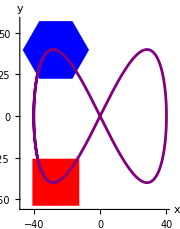

```mathematica
M7[0,0]
```

```mathematica
Rot7[O1_,O2_,OTraj_,Traj_,trange_]:=Module[{TAll,MTran1,MTran2,Trans1,Trans2,t1,a1,GAll},
GAll[t1_,a1_]:=Graphics[{GeometricTransformation[O1,Composition[TranslationTransform[Traj[-t1+trange]],RotationTransform[a1]]],GeometricTransformation[O2,Composition[TranslationTransform[Traj[t1-trange]],RotationTransform[a1]]],OTraj},Axes->True,PlotRange->60];
GAll]
```

```mathematica
Manipulate[Rot7[{Red,RegularPolygon[{0,0},20,4]},{Blue,RegularPolygon[{0,0},20,6]},o62,TrajNew,trange][t/5,t],{t,-20,20}]
```